# Importacion de datos experimentales

```mathematica
SetDirectory["C:\Users\ameat\OneDrive\Música\Documentos\Calculos Mie\Respuesta de los materiales"]
```

```mathematica
"C:\\Users\\ameat\\OneDrive\\Música\\Documentos\\Calculos Mie\\Respuesta de los materiales"
```

C:\Users\ameat\OneDrive\Música\Documentos\Calculos Mie\Respuesta de los materiales

```mathematica
(**Importar datos de Au, Al, Ag, Si y SiC**)
AuTxt= Import["Au_J&C.txt","Table"]; (**refractive index**)
AgTxt= Import["1-Ag_Johnson&Christy.txt","Table"]; (**refractive index**)
SiTxt= Import["Si_Palik.txt","Table"]; (**dielectric function**)
SiCTxt= Import["SiC-6H_Palik_Jose.dat","Table"];
```

```mathematica
(**Número de puntos que se tienen**)
NDatAu=AuTxt[[1]][[1]]; (**Número de datos de Au**)
NDatAg=AgTxt[[1]][[1]]; (**Número de datos de Al**)
NDatSi=SiTxt[[1]][[1]];(**Número de datos de Si**)
NDatSiC=SiCTxt[[1]][[1]]; (**Número de datos de SiC**)
(**Selección de los puntos sin las indicaciones del documento txt**)
AuData=AuTxt[[3;;2+NDatAu]]; (**Conjunto de datos de Au**)
AgData=AgTxt[[3;;2+NDatAg]]; (**Conjunto de datos de Au**)
SiData=SiTxt[[3;;2+NDatSi]]; (**Conjunto de datos de Au**)
SiCData=SiCTxt[[3;;2+NDatSiC]]; (**Conjunto de datos de Au**)
```

```mathematica
(**Parte real e imaginaria del índice de refracción Au**)
nAuData=Table[{AuData[[i]][[1]],AuData[[i]][[2]]},{i,1,NDatAu}];
kAuData=Table[{AuData[[i]][[1]],AuData[[i]][[3]]},{i,1,NDatAu}];
(**Parte real e imaginaria del índice de refracción Ag**)
nAgData=Table[{AgData[[i]][[1]],AgData[[i]][[2]]},{i,1,NDatAg}];
kAgData=Table[{AgData[[i]][[1]],AgData[[i]][[3]]},{i,1,NDatAg}];
(**Parte real e imaginaria del índice de refracción Si**)
ϵreSiData=Table[{SiData[[i]][[1]],SiData[[i]][[2]]},{i,1,NDatSi}];
ϵimSiData=Table[{SiData[[i]][[1]],SiData[[i]][[3]]},{i,1,NDatSi}];
(**Parte real e imaginaria del índice de refracción Si**)
nSiData=Table[{SiData[[i]][[1]],Re[Sqrt[SiData[[i]][[2]]+I*SiData[[i]][[3]]]]},{i,1,NDatSi}];
kSiData=Table[{SiData[[i]][[1]],Im[Sqrt[SiData[[i]][[2]]+I*SiData[[i]][[3]]]]},{i,1,NDatSi}];
(**Parte real e imaginaria del índice de refracción Si**)
nSiCData=Table[{SiCData[[i]][[1]],SiCData[[i]][[2]]},{i,1,NDatSiC}];
kSiCData=Table[{SiCData[[i]][[1]],SiCData[[i]][[3]]},{i,1,NDatSiC}];
```

## Interpolacion

```mathematica
nAu=Interpolation[nAuData,Method->"Spline"];
kAu=Interpolation[kAuData,Method->"Spline"];
nAg=Interpolation[nAgData,Method->"Spline"];
kAg=Interpolation[kAgData,Method->"Spline"];
nSi =Interpolation[nSiData,Method->"Spline"];
kSi=Interpolation[kSiData,Method->"Spline"];
nSiC =Interpolation[nSiCData,Method->"Spline"];
kSiC=Interpolation[kSiCData,Method->"Spline"];
```

## Indice de refraccion

```mathematica
rfindxAu[hw_]:=nAu[hw]+I*kAu[hw]
rfindxAg[hw_]:=nAg[hw]+I*kAg[hw]
rfindxSi[hw_]:=nSi[hw]+I*kSi[hw]
rfindxSiC[hw_]:=nSiC[hw]+I*kSiC[hw]
```

```mathematica
hp=4.135667731×10^(-15);"eV";
c=299792458*10^9;"nm/s";
hbar=6.582119569*10^(-16); (* eV s *) 
attosec=10^(-18);
atomicunitofspeed = 2.1877 ;(* x 10^8 cm/s*) (*value from Atomic units table.jpg*)
atomicunitoftime=24.189;(*as*)
fermivelocityofaluminum=2.03; (* x 10^8 cm/s*) (*value from Ashcroft page 38*)
alvf=fermivelocityofaluminum/atomicunitofspeed ;(*Al Fermi velocity in atomic units*)
nanometer=100/5.29177210903; (*nanometer in atomic units *)
electronVolt=0.0367493;
cSpeedLight=137.036;
qElectronCharge=-1;
electronCharge=-1;
(*Drude Aluminium*)
ωplasma= 13.142*electronVolt;(*Al*)                                                  
Γdamping=0.197*electronVolt;(*Al*)

(*Daniel Silver*)
(*ωplasma= 9.055*electronVolt;(*Ag*)                                                  
Γdamping=0.5*electronVolt;(*Ag*)*)

ΓsizeAla1nm = alvf/nanometer (*damping size correction for an a=1nm Al sphere Γc=A*(vF/R) with A=1 and R Np radius*)(* Kreibig book optical properties of metals pag 81*);
atomicunitofdistance=5.2918*10^-11;
SIunitofpolarizability=4π*(atomicunitofdistance)^3/(atomicunitoftime*attosec)*10^11;(*4π comes from the fact αSI = 4π αcgs*)
SIunitofforce=8.2387234983*10^-8;(*N*)
SIunitofmomentum=1.9928519128789674*10^-24;
```

## Drude model

```mathematica
ϵDrudeAl[ωFreq_]=(1-ωplasma^2/(ωFreq(ωFreq + I (Γdamping))));
γLorentz[vel_]=1/(√(1-(vel/cSpeedLight)^2));
kWaveNumber[ωFreq_]=ωFreq/cSpeedLight;
Lorentzian[ω_,ω0_,Γ_,A_]:=(A*electronVolt^2)/(-ω^2+(ω0*electronVolt)^2-I ω (Γ*electronVolt)) (*In atomic units*)
```

```mathematica
ϵDS[w_,wp_,γ_]:= 1 - wp^2/((w)*(w+ⅈ*γ)); (**permititividad en función de la frecuencia**) 
nDS[w_,wp_,gamma_]:=Sqrt[ϵDS[w,wp,gamma]]; (**índice de refracción con modelo de Drude en función de la frecuencia**) 
nDS1[0,w_]:=√ϵDS[w,13.144,0.19716];
NAlDeV[w_]:=Re[nDS1[0,w]];
KAlDeV[w_]:=Im[nDS1[0,w]];
```

# Modelo de Lorentz

```mathematica
Lorentzian[w_,wp_,γ_,w0_]:= 1 - wp^2/(-w^2+w0^2-ⅈ*w*γ); (**permititividad en función de la frecuencia**)
```

```mathematica
dielec[w_,wp_,γ_,w0_]:=wp^2/(-w^2+w0^2-ⅈ*w*γ)-wp^2/((w)*(w+ⅈ*γ))
```

# Gráficas función dieléctrica

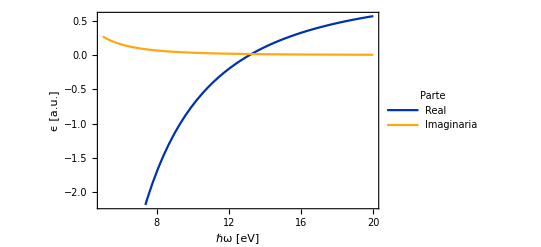

```mathematica
(***Al***)
Plot[{Re[ϵDS[w,13.144,0.19716]],Im[ϵDS[w,13.144,0.19716]]},{w,5,20},Frame->True, PlotStyle->{RGBColor[0.,0.2,0.67],RGBColor[1.,0.66,0.08]},FrameLabel->{{"StyleBox[\"ϵ\",FontSize->18] [a.u.]",None},{"ℏω [eV]","λ [nm]"}},FrameStyle->Black,LabelStyle->{Directive[Bold,Black],FontFamily-> "Helvetica",FontSize->14}, PlotLegends->Placed[LineLegend[{"Real","Imaginaria"},LegendLabel->"Parte",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}]]
```

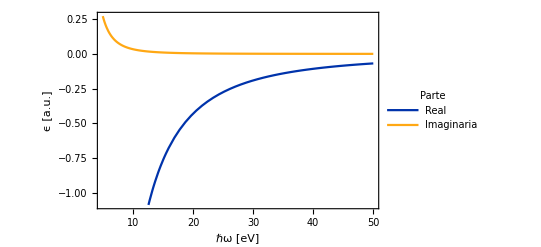

```mathematica
(***Al con lorenziana ***)
Plot[{Re[dielec[w,13.144,0.19716,540]],Im[dielec[w,13.144,0.19716,540]]},{w,5,50},Frame->True, PlotStyle->{RGBColor[0.,0.2,0.67],RGBColor[1.,0.66,0.08]},FrameLabel->{{"ϵ [a.u.]",None},{"ℏω [eV]","λ [nm]"}},FrameStyle->Black,LabelStyle->{Directive[Bold,Black],FontFamily-> "Helvetica",FontSize->14}, PlotLegends->Placed[LineLegend[{"Real","Imaginaria"},LegendLabel->"Parte",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}]]
```

```mathematica
ϵWernerAu[ω_]:=1+
Lorentzian[ω,0,.2,113.1]
```

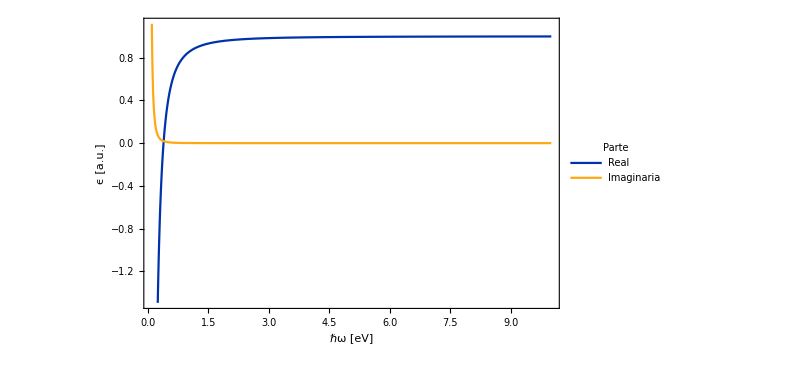

```mathematica
(***Au***)
Plot[{Re[ϵWernerAu[w]],Im[ϵWernerAu[w]]},{w,0.1,10},Frame->True, PlotStyle->{RGBColor[0.,0.2,0.67],RGBColor[1.,0.66,0.08]},FrameLabel->{{"ϵ [a.u.]",None},{"ℏω [eV]","λ [nm]"}},FrameStyle->Black,LabelStyle->{Directive[Bold,Black],FontFamily-> "Helvetica",FontSize->14}, PlotLegends->Placed[LineLegend[{"Real","Imaginaria"},LegendLabel->"Parte",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}]]
```